```mathematica
(**Function for extracting RowBox from documentation**)
Clear[extractFunctionFromRowBox]
extractFunctionFromRowBox[box_]:=ToExpression[Catch @ ReplaceAll[box,f_RowBox:>Throw[f]],StandardForm,Hold]
```

```mathematica
(**Find function example in documentation as RowBox**)
Clear[findFunctionsExampleInDoc]
findFunctionsExampleInDoc[functionName_]:=Flatten[Lookup[WolframLanguageData[functionName,"DocumentationExampleInputs"],"BasicExamples"]]
```

```mathematica
(**Pick a random sample from documentation about functionName**)
Clear[extractRandomFunction]
Clear[extractNFunction]
extractRandomFunction[functionName_]:=extractFunctionFromRowBox[RandomChoice[findFunctionsExampleInDoc[functionName]]]
extractNFunction[functionName_,n_]/; 0<n&&n≤Length[findFunctionsExampleInDoc[functionName]]:=extractFunctionFromRowBox[findFunctionsExampleInDoc[functionName][[n]]]
```

```mathematica
(**Usage example**)
extractRandomFunction["Sin"]
extractRandomFunction["Select"]
```

Hold[Series[Sin[x],{x,0,10}]]

Hold[Select[Association[a→1,b→2,c→3,d→4],#1>2&]]

```mathematica
(**Substitute part of the function with ?**)
Clear[tweakFunction]
(**SetAttributes[tweakFunction,HoldFirst]**)
ClearAttributes[tweakFunction,HoldFirst]
tweakFunction[Hold[expr_]]:=With[
{l=RandomInteger[{0,Length[Unevaluated[expr]]}]},
ReplacePart[HoldForm[expr],{1,l}->Placeholder["?"]]]
(**Better use this one the other is not fair!**)
tweakFunction[Hold[expr_],n_]/; 0≤ n≤ Length[Unevaluated[expr]]:=ReplacePart[HoldForm[expr],{1,n}->Placeholder["?"]]
(**this is very unsafe to use but wonderful**)
tweakFunction[Hold[expr_],n_List]:=With[
{s=n/.List->Sequence},
ReplacePart[HoldForm[expr],{1,s}->Placeholder["?"]]]
```

```mathematica
(**Usage example**)
tweakFunction[extractNFunction["NestGraph",2],2]
```

NestGraph[Mod[#1^2+1,10]&,?,VertexLabels→Name]

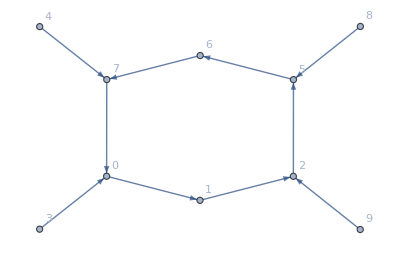

```mathematica
NestGraph[Mod[#1^2+1,10]&,Range[0,9],VertexLabels->"Name"]
```

```mathematica
tweakFunction[extractNFunction["NestGraph",2],{1,1,1}]
```

NestGraph[Mod[?,10]&,Range[0,9],VertexLabels→Name]

```mathematica
Table[extractNFunction["NestGraph",i],{i,1,Length[findFunctionsExampleInDoc["NestGraph"]]}]
```

{Hold[NestGraph[f,x,3,VertexLabels→Name,ImagePadding→40]],Hold[NestGraph[Mod[#1^2+1,10]&,Range[0,9],VertexLabels→Name]],Hold[NestGraph[{f[#1],g[#1]}&,x,3,VertexLabels→Name]],Hold[NestGraph[#1[BorderingCountries]&,Switzerland,2,VertexLabels→Name]]}

```mathematica
extractNFunction["ImageCompose",2]
```

Hold[ImageCompose[-Graphics-,-Graphics-,Scaled[{0.5,0.9}]]]

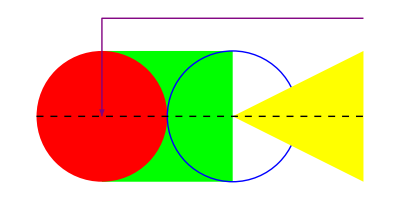
Hold[-Graphics-]

```mathematica
extractNFunction["Graphics",1]
```

```mathematica
(**This function sobstitute all the keyword in pattern_ as Placeholder.**)
Clear[removeExpressionPart]
SetAttributes[removeExpressionPart,HoldAllComplete]
(**pattern=_Symbol?SymbolQ**)
pattern=_Image|_Graph|_Graphics|_Graphics3D;
removeExpressionPart[expr_,pattern_]:=expr/.pattern->Placeholder[]
```

```mathematica
removeExpressionPart[Hold[-Graphics-],pattern]
```

Hold[□]

```mathematica
positionsOfRemovablePart[removeExpressionPart[Hold[ImageCompose[-Graphics-,-Graphics-,Scaled[{0.5,0.9}]]],pattern]]
```

{{0}:>ImageCompose,{3,0}:>Scaled,{3,1,1}:>0.5,{3,1,2}:>0.9,{3,1}:>□[0.5,0.9],{3}:>Scaled[□[0.5,0.9]],{0}:>ImageCompose[□,□,Scaled[□[0.5,0.9]]]}

```mathematica
ReplaceAll[Hold[ImageCompose[□,□,Scaled[{0.5,0.9}]]]]
```

ReplaceAll[Hold[ImageCompose[□,□,Scaled[{0.5,0.9}]]]]

```mathematica
(**
 This function find the position of all the expressione that can be removed from a function 
 making it harder to guess but still meaningful.
It avoid selecting path to Placeholder, Hold, Rule,RuleDelayed, List, etc..
**)
Clear[positionsOfRemovablePart]
SetAttributes[positionsOfRemovablePart,HoldAllComplete]
avoidedEspression = Placeholder|_Placeholder|Hold|Rule|RuleDelayed|List|_List;
positionsOfRemovablePart[exrp_]:=With[
{pos=Position[exrp,Except[avoidedEspression]]},
Map[Extract[exrp,#,Function[i,If[Length[Rest[#]]==0,{0},Rest[#]]:>i,HoldFirst]]&,pos][[1;;-2]]
]
```

```mathematica
positionsOfRemovablePart[Hold[List[1,2,3]]]
```

{{1}:>1,{2}:>2,{3}:>3}

```mathematica
Clear[listRemovablePartFromEspression]
SetAttributes[listRemovablePartFromEspression,HoldAllComplete]
listRemovablePartFromEspression[espr_,pattern_]:=positionsOfRemovablePart[removeExpressionPart[espr,pattern]]
```

```mathematica
(**Example random extraction**)
Clear[g]
Clear[l]
Clear[p]
g=extractRandomFunction["ImageCompose"]
l=listRemovablePartFromEspression[g,pattern]
p=First[l[[RandomInteger[{1,Length[l]}]]]]
tweakFunction[g,p]
ReleaseHold[g]
```

```mathematica
(**Test Case all possibility form **)
Clear[g]
Clear[l]
Clear[p]
g=Hold[f[g[h[{x,y}]]]];
Print[g]
l=listRemovablePartFromEspression[g,pattern];
Print[l]
p=First[l[[RandomInteger[{1,Length[l]}]]]];
Print[p]
r=Table[tweakFunction[g,First[l[[i]]]],{i,1,Length[l]}];
Print[r]
Print[ReleaseHold[g]]
```

Hold[f[g[h[{x,y}]]]]

{{0}:>f,{1,0}:>g,{1,1,0}:>h,{1,1,1,1}:>x,{1,1,1,2}:>y,{1,1}:>h[{x,y}],{1}:>g[h[{x,y}]],{0}:>f[g[h[{x,y}]]]}

{1,1,0}

{?[g[h[{x,y}]]],f[?[h[{x,y}]]],f[g[?[{x,y}]]],f[g[h[{?,y}]]],f[g[h[{x,?}]]],f[g[?]],f[?],?[g[h[{x,y}]]]}

f[Hold[f[g[h[{x,y}]]]][h[{x,y}]]]

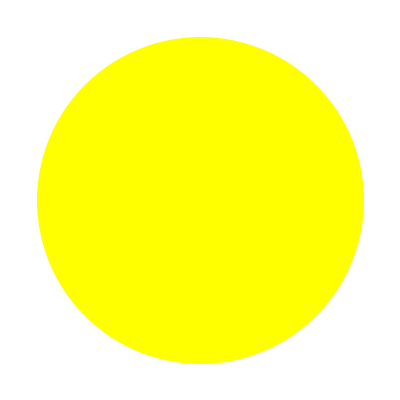
```mathematica
(**Weird stuff**)
listRemovablePartFromEspression[Hold[ImageCompose[-Graphics-,{-Graphics-,0.5}]],pattern]
```